Underdamped 1

```mathematica
$Assumptions={τ>0,γ>0,ω0>0,√(ω0^2-γ^2/4)>0,τ>=t>=0,τ>=u>=0};
```

```mathematica
Psi[t_]=Exp[-γ/2 Abs[t]](Cos[√(ω0^2-γ^2/4)t]+γ/(2 √(ω0^2-γ^2/4))Sin[√(ω0^2-γ^2/4)Abs[t]]);
dPsi[t_]=-(2 ⅇ^(-1/2 γ Abs[t]) ω0^2 Sin[t √(-γ^2/4+ω0^2)])/(√(-γ^2+4 ω0^2));
ddPsi[t_]=-ⅇ^(-1/2 γ Abs[t]) ω0^2 Cos[t √(-γ^2/4+ω0^2)]+(ⅇ^(-1/2 γ Abs[t]) γ ω0^2 Sin[Abs[t] √(-γ^2/4+ω0^2)])/(√(-γ^2+4 ω0^2));
```

```mathematica
f[s_]=-1/(s LaplaceTransform[ddPsi[t],t,s]);

c0=SeriesCoefficient[f[s],{s,0,0}];

c1=SeriesCoefficient[f[s],{s,0,1}];

c2=SeriesCoefficient[f[s],{s,0,2}];
```

```mathematica
Clear[γ,ω0,Wh3]
τR=γ/ω0^2;
gs[t_]=1/(√(π 0.0001))Exp[-(t/0.01)^2];
g[t_]=(t+τR)/(τ+2τR);
h1[t_]=t/τ;
h2[t_]=t/τ+Sin[π t/τ];
h3[t_]=t/τ+4(t/τ-1/2)^3;
```

```mathematica
Wh3[τ_]=Expand[FullSimplify[Psi[0]/2+Integrate[dPsi[τ-t]h3[t],{t,0,τ}]-1/2 Integrate[ddPsi[t-u]h3[t]h3[u],{t,0,τ},{u,0,τ}]]];
```

```mathematica
Wh1[τ_]=Expand[FullSimplify[Psi[0]/2+Integrate[dPsi[τ-t]h1[t],{t,0,τ}]-1/2 Integrate[ddPsi[t-u]h1[t]h1[u],{t,0,τ},{u,0,τ}]]]
```

```mathematica
Wh2[τ_]=Expand[FullSimplify[Psi[0]/2+Integrate[dPsi[τ-t]h2[t],{t,0,τ}]-1/2 Integrate[ddPsi[t-u]h2[t]h2[u],{t,0,τ},{u,0,τ}]]]
```

```mathematica
W0[τ_]=Expand[FullSimplify[Psi[0]/2+Integrate[dPsi[τ-t]g[t],{t,0,τ}]-1/2 Integrate[ddPsi[t-u]g[t]g[u],{t,0,τ},{u,0,τ}]]];
```

```mathematica
W1[τ_]=Expand[FullSimplify[Psi[0]/2+1/2 Integrate[dPsi[τ-t]g[t],{t,0,τ}]+(c0(dPsi[τ]-dPsi[0]))/(2(τ+2τR))]];
```

```mathematica
Wh1[τ_]=-γ^2/(τ^2 ω0^4)+1/(τ^2 ω0^2)+γ/(τ ω0^2)+(ⅇ^(-(γ τ)/2) γ^2 Cos[1/2 τ √(-γ^2+4 ω0^2)])/(τ^2 ω0^4)-(ⅇ^(-(γ τ)/2) Cos[1/2 τ √(-γ^2+4 ω0^2)])/(τ^2 ω0^2)+(ⅇ^(-(γ τ)/2) γ^3 Sin[1/2 τ √(-γ^2+4 ω0^2)])/(τ^2 ω0^4 √(-γ^2+4 ω0^2))-(3 ⅇ^(-(γ τ)/2) γ Sin[1/2 τ √(-γ^2+4 ω0^2)])/(τ^2 ω0^2 √(-γ^2+4 ω0^2));
Wh2[τ_]=-(4 π^6)/((π^4+τ^4 ω0^4+π^2 τ^2 (γ^2-2 ω0^2))^2)-(4 π^6 γ τ)/((π^4+τ^4 ω0^4+π^2 τ^2 (γ^2-2 ω0^2))^2)-(10 π^4 γ^2 τ^2)/((π^4+τ^4 ω0^4+π^2 τ^2 (γ^2-2 ω0^2))^2)-(4 π^4 γ^3 τ^3)/((π^4+τ^4 ω0^4+π^2 τ^2 (γ^2-2 ω0^2))^2)-(2 π^2 γ^4 τ^4)/((π^4+τ^4 ω0^4+π^2 τ^2 (γ^2-2 ω0^2))^2)-(2 π^6 γ^4)/(ω0^4 (π^4+τ^4 ω0^4+π^2 τ^2 (γ^2-2 ω0^2))^2)-(π^8 γ^2)/(τ^2 ω0^4 (π^4+τ^4 ω0^4+π^2 τ^2 (γ^2-2 ω0^2))^2)-(π^4 γ^6 τ^2)/(ω0^4 (π^4+τ^4 ω0^4+π^2 τ^2 (γ^2-2 ω0^2))^2)+(6 π^6 γ^2)/(ω0^2 (π^4+τ^4 ω0^4+π^2 τ^2 (γ^2-2 ω0^2))^2)+π^8/(τ^2 ω0^2 (π^4+τ^4 ω0^4+π^2 τ^2 (γ^2-2 ω0^2))^2)+(π^8 γ)/(τ ω0^2 (π^4+τ^4 ω0^4+π^2 τ^2 (γ^2-2 ω0^2))^2)+(2 π^6 γ^3 τ)/(ω0^2 (π^4+τ^4 ω0^4+π^2 τ^2 (γ^2-2 ω0^2))^2)+(5 π^4 γ^4 τ^2)/(ω0^2 (π^4+τ^4 ω0^4+π^2 τ^2 (γ^2-2 ω0^2))^2)+(π^4 γ^5 τ^3)/(ω0^2 (π^4+τ^4 ω0^4+π^2 τ^2 (γ^2-2 ω0^2))^2)+(6 π^4 τ^2 ω0^2)/((π^4+τ^4 ω0^4+π^2 τ^2 (γ^2-2 ω0^2))^2)+(π^6 τ^2 ω0^2)/((π^4+τ^4 ω0^4+π^2 τ^2 (γ^2-2 ω0^2))^2)+(6 π^4 γ τ^3 ω0^2)/((π^4+τ^4 ω0^4+π^2 τ^2 (γ^2-2 ω0^2))^2)+(π^6 γ τ^3 ω0^2)/(2 (π^4+τ^4 ω0^4+π^2 τ^2 (γ^2-2 ω0^2))^2)+(6 π^2 γ^2 τ^4 ω0^2)/((π^4+τ^4 ω0^4+π^2 τ^2 (γ^2-2 ω0^2))^2)+(2 π^2 γ^3 τ^5 ω0^2)/((π^4+τ^4 ω0^4+π^2 τ^2 (γ^2-2 ω0^2))^2)+(π^4 γ^3 τ^5 ω0^2)/(2 (π^4+τ^4 ω0^4+π^2 τ^2 (γ^2-2 ω0^2))^2)-(4 π^2 τ^4 ω0^4)/((π^4+τ^4 ω0^4+π^2 τ^2 (γ^2-2 ω0^2))^2)-(2 π^4 τ^4 ω0^4)/((π^4+τ^4 ω0^4+π^2 τ^2 (γ^2-2 ω0^2))^2)-(4 π^2 γ τ^5 ω0^4)/((π^4+τ^4 ω0^4+π^2 τ^2 (γ^2-2 ω0^2))^2)-(π^4 γ τ^5 ω0^4)/((π^4+τ^4 ω0^4+π^2 τ^2 (γ^2-2 ω0^2))^2)-(γ^2 τ^6 ω0^4)/((π^4+τ^4 ω0^4+π^2 τ^2 (γ^2-2 ω0^2))^2)-(π^2 γ^2 τ^6 ω0^4)/((π^4+τ^4 ω0^4+π^2 τ^2 (γ^2-2 ω0^2))^2)+(τ^6 ω0^6)/((π^4+τ^4 ω0^4+π^2 τ^2 (γ^2-2 ω0^2))^2)+(π^2 τ^6 ω0^6)/((π^4+τ^4 ω0^4+π^2 τ^2 (γ^2-2 ω0^2))^2)+(γ τ^7 ω0^6)/((π^4+τ^4 ω0^4+π^2 τ^2 (γ^2-2 ω0^2))^2)+(π^2 γ τ^7 ω0^6)/(2 (π^4+τ^4 ω0^4+π^2 τ^2 (γ^2-2 ω0^2))^2)+(4 ⅇ^(-(γ τ)/2) π^6 Cos[1/2 τ √(-γ^2+4 ω0^2)])/((π^4+τ^4 ω0^4+π^2 τ^2 (γ^2-2 ω0^2))^2)+(10 ⅇ^(-(γ τ)/2) π^4 γ^2 τ^2 Cos[1/2 τ √(-γ^2+4 ω0^2)])/((π^4+τ^4 ω0^4+π^2 τ^2 (γ^2-2 ω0^2))^2)+(2 ⅇ^(-(γ τ)/2) π^2 γ^4 τ^4 Cos[1/2 τ √(-γ^2+4 ω0^2)])/((π^4+τ^4 ω0^4+π^2 τ^2 (γ^2-2 ω0^2))^2)+(2 ⅇ^(-(γ τ)/2) π^6 γ^4 Cos[1/2 τ √(-γ^2+4 ω0^2)])/(ω0^4 (π^4+τ^4 ω0^4+π^2 τ^2 (γ^2-2 ω0^2))^2)+(ⅇ^(-(γ τ)/2) π^8 γ^2 Cos[1/2 τ √(-γ^2+4 ω0^2)])/(τ^2 ω0^4 (π^4+τ^4 ω0^4+π^2 τ^2 (γ^2-2 ω0^2))^2)+(ⅇ^(-(γ τ)/2) π^4 γ^6 τ^2 Cos[1/2 τ √(-γ^2+4 ω0^2)])/(ω0^4 (π^4+τ^4 ω0^4+π^2 τ^2 (γ^2-2 ω0^2))^2)-(6 ⅇ^(-(γ τ)/2) π^6 γ^2 Cos[1/2 τ √(-γ^2+4 ω0^2)])/(ω0^2 (π^4+τ^4 ω0^4+π^2 τ^2 (γ^2-2 ω0^2))^2)-(ⅇ^(-(γ τ)/2) π^8 Cos[1/2 τ √(-γ^2+4 ω0^2)])/(τ^2 ω0^2 (π^4+τ^4 ω0^4+π^2 τ^2 (γ^2-2 ω0^2))^2)-(5 ⅇ^(-(γ τ)/2) π^4 γ^4 τ^2 Cos[1/2 τ √(-γ^2+4 ω0^2)])/(ω0^2 (π^4+τ^4 ω0^4+π^2 τ^2 (γ^2-2 ω0^2))^2)-(6 ⅇ^(-(γ τ)/2) π^4 τ^2 ω0^2 Cos[1/2 τ √(-γ^2+4 ω0^2)])/((π^4+τ^4 ω0^4+π^2 τ^2 (γ^2-2 ω0^2))^2)+(ⅇ^(-(γ τ)/2) π^6 τ^2 ω0^2 Cos[1/2 τ √(-γ^2+4 ω0^2)])/((π^4+τ^4 ω0^4+π^2 τ^2 (γ^2-2 ω0^2))^2)-(6 ⅇ^(-(γ τ)/2) π^2 γ^2 τ^4 ω0^2 Cos[1/2 τ √(-γ^2+4 ω0^2)])/((π^4+τ^4 ω0^4+π^2 τ^2 (γ^2-2 ω0^2))^2)+(4 ⅇ^(-(γ τ)/2) π^2 τ^4 ω0^4 Cos[1/2 τ √(-γ^2+4 ω0^2)])/((π^4+τ^4 ω0^4+π^2 τ^2 (γ^2-2 ω0^2))^2)-(2 ⅇ^(-(γ τ)/2) π^4 τ^4 ω0^4 Cos[1/2 τ √(-γ^2+4 ω0^2)])/((π^4+τ^4 ω0^4+π^2 τ^2 (γ^2-2 ω0^2))^2)+(ⅇ^(-(γ τ)/2) γ^2 τ^6 ω0^4 Cos[1/2 τ √(-γ^2+4 ω0^2)])/((π^4+τ^4 ω0^4+π^2 τ^2 (γ^2-2 ω0^2))^2)-(ⅇ^(-(γ τ)/2) π^2 γ^2 τ^6 ω0^4 Cos[1/2 τ √(-γ^2+4 ω0^2)])/((π^4+τ^4 ω0^4+π^2 τ^2 (γ^2-2 ω0^2))^2)-(ⅇ^(-(γ τ)/2) τ^6 ω0^6 Cos[1/2 τ √(-γ^2+4 ω0^2)])/((π^4+τ^4 ω0^4+π^2 τ^2 (γ^2-2 ω0^2))^2)+(ⅇ^(-(γ τ)/2) π^2 τ^6 ω0^6 Cos[1/2 τ √(-γ^2+4 ω0^2)])/((π^4+τ^4 ω0^4+π^2 τ^2 (γ^2-2 ω0^2))^2)+(12 ⅇ^(-(γ τ)/2) π^6 γ Sin[1/2 τ √(-γ^2+4 ω0^2)])/(√(-γ^2+4 ω0^2) (π^4+τ^4 ω0^4+π^2 τ^2 (γ^2-2 ω0^2))^2)+(18 ⅇ^(-(γ τ)/2) π^4 γ^3 τ^2 Sin[1/2 τ √(-γ^2+4 ω0^2)])/(√(-γ^2+4 ω0^2) (π^4+τ^4 ω0^4+π^2 τ^2 (γ^2-2 ω0^2))^2)+(2 ⅇ^(-(γ τ)/2) π^2 γ^5 τ^4 Sin[1/2 τ √(-γ^2+4 ω0^2)])/(√(-γ^2+4 ω0^2) (π^4+τ^4 ω0^4+π^2 τ^2 (γ^2-2 ω0^2))^2)+(2 ⅇ^(-(γ τ)/2) π^6 γ^5 Sin[1/2 τ √(-γ^2+4 ω0^2)])/(ω0^4 √(-γ^2+4 ω0^2) (π^4+τ^4 ω0^4+π^2 τ^2 (γ^2-2 ω0^2))^2)+(ⅇ^(-(γ τ)/2) π^8 γ^3 Sin[1/2 τ √(-γ^2+4 ω0^2)])/(τ^2 ω0^4 √(-γ^2+4 ω0^2) (π^4+τ^4 ω0^4+π^2 τ^2 (γ^2-2 ω0^2))^2)+(ⅇ^(-(γ τ)/2) π^4 γ^7 τ^2 Sin[1/2 τ √(-γ^2+4 ω0^2)])/(ω0^4 √(-γ^2+4 ω0^2) (π^4+τ^4 ω0^4+π^2 τ^2 (γ^2-2 ω0^2))^2)-(10 ⅇ^(-(γ τ)/2) π^6 γ^3 Sin[1/2 τ √(-γ^2+4 ω0^2)])/(ω0^2 √(-γ^2+4 ω0^2) (π^4+τ^4 ω0^4+π^2 τ^2 (γ^2-2 ω0^2))^2)-(3 ⅇ^(-(γ τ)/2) π^8 γ Sin[1/2 τ √(-γ^2+4 ω0^2)])/(τ^2 ω0^2 √(-γ^2+4 ω0^2) (π^4+τ^4 ω0^4+π^2 τ^2 (γ^2-2 ω0^2))^2)-(7 ⅇ^(-(γ τ)/2) π^4 γ^5 τ^2 Sin[1/2 τ √(-γ^2+4 ω0^2)])/(ω0^2 √(-γ^2+4 ω0^2) (π^4+τ^4 ω0^4+π^2 τ^2 (γ^2-2 ω0^2))^2)-(18 ⅇ^(-(γ τ)/2) π^4 γ τ^2 ω0^2 Sin[1/2 τ √(-γ^2+4 ω0^2)])/(√(-γ^2+4 ω0^2) (π^4+τ^4 ω0^4+π^2 τ^2 (γ^2-2 ω0^2))^2)-(ⅇ^(-(γ τ)/2) π^6 γ τ^2 ω0^2 Sin[1/2 τ √(-γ^2+4 ω0^2)])/(√(-γ^2+4 ω0^2) (π^4+τ^4 ω0^4+π^2 τ^2 (γ^2-2 ω0^2))^2)-(10 ⅇ^(-(γ τ)/2) π^2 γ^3 τ^4 ω0^2 Sin[1/2 τ √(-γ^2+4 ω0^2)])/(√(-γ^2+4 ω0^2) (π^4+τ^4 ω0^4+π^2 τ^2 (γ^2-2 ω0^2))^2)+(12 ⅇ^(-(γ τ)/2) π^2 γ τ^4 ω0^4 Sin[1/2 τ √(-γ^2+4 ω0^2)])/(√(-γ^2+4 ω0^2) (π^4+τ^4 ω0^4+π^2 τ^2 (γ^2-2 ω0^2))^2)-(2 ⅇ^(-(γ τ)/2) π^4 γ τ^4 ω0^4 Sin[1/2 τ √(-γ^2+4 ω0^2)])/(√(-γ^2+4 ω0^2) (π^4+τ^4 ω0^4+π^2 τ^2 (γ^2-2 ω0^2))^2)+(ⅇ^(-(γ τ)/2) γ^3 τ^6 ω0^4 Sin[1/2 τ √(-γ^2+4 ω0^2)])/(√(-γ^2+4 ω0^2) (π^4+τ^4 ω0^4+π^2 τ^2 (γ^2-2 ω0^2))^2)-(ⅇ^(-(γ τ)/2) π^2 γ^3 τ^6 ω0^4 Sin[1/2 τ √(-γ^2+4 ω0^2)])/(√(-γ^2+4 ω0^2) (π^4+τ^4 ω0^4+π^2 τ^2 (γ^2-2 ω0^2))^2)-(3 ⅇ^(-(γ τ)/2) γ τ^6 ω0^6 Sin[1/2 τ √(-γ^2+4 ω0^2)])/(√(-γ^2+4 ω0^2) (π^4+τ^4 ω0^4+π^2 τ^2 (γ^2-2 ω0^2))^2)+(3 ⅇ^(-(γ τ)/2) π^2 γ τ^6 ω0^6 Sin[1/2 τ √(-γ^2+4 ω0^2)])/(√(-γ^2+4 ω0^2) (π^4+τ^4 ω0^4+π^2 τ^2 (γ^2-2 ω0^2))^2);
W0[τ_]=(2 γ^2)/((2 γ+τ ω0^2)^2)+ω0^2/((2 γ+τ ω0^2)^2)+(γ τ ω0^2)/((2 γ+τ ω0^2)^2)-(ⅇ^(-(γ τ)/2) ω0^2 Cos[1/2 τ √(-γ^2+4 ω0^2)])/((2 γ+τ ω0^2)^2)+(ⅇ^(-(γ τ)/2) γ ω0^2 Sin[1/2 τ √(-γ^2+4 ω0^2)])/(√(-γ^2+4 ω0^2) (2 γ+τ ω0^2)^2);
W1[τ_]=γ/(2 γ+τ ω0^2);
```

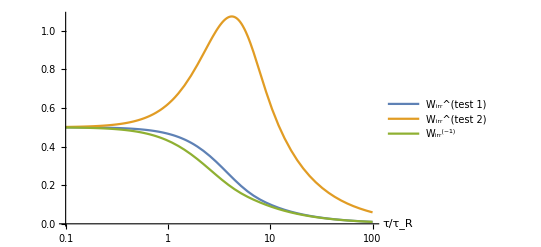

```mathematica
γ=1;
ω0=1;
τR=γ/ω0^2;
LogLinearPlot[{Legended[Wh1[τ],"W_irr^(test 1)"],Legended[Wh2[τ],"W_irr^(test 2)"],Legended[W0[τ],"W_irr^(-1)"]},{τ,0.1,100},PlotRange->Full,AxesLabel->{"τ/τ_R"},PlotLegends->Placed[{},{Right,Center}]]
Clear[τR,γ,ω0]
```

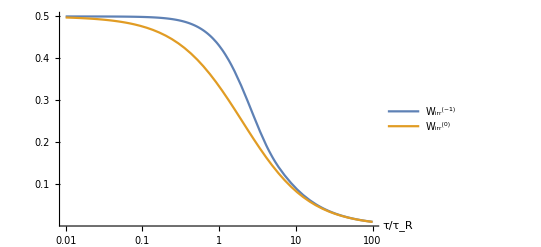

```mathematica
γ=1;
ω0=1;
τR=γ/ω0^2;
LogLinearPlot[{Legended[W0[τ],"W_irr^(-1)"],Legended[W1[τ],"W_irr^(0)"]},{τ,0.01,100},PlotRange->Full,AxesLabel->{"τ/τ_R"},PlotLegends->Placed[{},{Right,Center}]]
Clear[τR,γ,ω0]
```

```mathematica
γ=1;
ω0=1;
τR=γ/ω0^2;

data0=List[];

Do[

aux=Table[{τ,W0[τ]},{τ,0.001*10^n,0.001*10^(n+1),0.001*10^(n-1)}];

Do[

data0=AppendTo[data0,aux[[j]]];

,{j,1,91}];

,{n,1,4}];


Export["/home/pnaze/Research/ongoing/PNOP/data/data_abs_psi2.dat",data];
```

```mathematica
γ=1;
ω0=1;
τR=γ/ω0^2;

data1=List[];

Do[

aux=Table[{τ,W1[τ]},{τ,0.001*10^n,0.001*10^(n+1),0.001*10^(n-1)}];

Do[

data1=AppendTo[data1,aux[[j]]];

,{j,1,91}];

,{n,1,4}];


Export["/home/pnaze/Research/ongoing/PNOP/data/data_abs_psi2.dat",data];
```

```mathematica
ϵ1[τ_]= Abs[(W1[τ]-W0[τ])/W1[τ]];
```

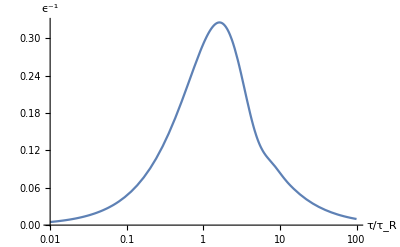

```mathematica
γ=1;
ω0=1;
τR=γ/ω0^2;
LogLinearPlot[ϵ1[τ],{τ,0.01,100},PlotRange->Full,AxesLabel->{"τ/τ_R","ϵ^-1"}]
Clear[τR,γ,ω0]
```

```mathematica
γ=1;
ω0=1;
τR=γ/ω0^2;

Do[

aux=Table[{τ,ϵ1[τ]},{τ,0.001*10^n,0.001*10^(n+1),0.001*10^(n-1)}];

Do[

data=AppendTo[data,aux[[j]]];

,{j,1,91}];

,{n,1,4}];

Export["/home/pnaze/Research/ongoing/PNOP/data/data_abs_psi2.dat",data];

Clear[τR,γ,ω0]
```

Testing

```mathematica
W0[τ_]=(2 γ^2)/((2 γ+τ ω0^2)^2)+ω0^2/((2 γ+τ ω0^2)^2)+(γ τ ω0^2)/((2 γ+τ ω0^2)^2)-(ⅇ^(-(γ τ)/2) ω0^2 Cos[1/2 τ √(-γ^2+4 ω0^2)])/((2 γ+τ ω0^2)^2)+(ⅇ^(-(γ τ)/2) γ ω0^2 Sin[1/2 τ √(-γ^2+4 ω0^2)])/(√(-γ^2+4 ω0^2) (2 γ+τ ω0^2)^2);

Wh3[τ_]=-(576 γ^6)/(τ^6 ω0^12)+(1152 a γ^6)/(τ^6 ω0^12)-(576 a^2 γ^6)/(τ^6 ω0^12)+(2880 γ^4)/(τ^6 ω0^10)-(5760 a γ^4)/(τ^6 ω0^10)+(2880 a^2 γ^4)/(τ^6 ω0^10)-(3456 γ^2)/(τ^6 ω0^8)+(6912 a γ^2)/(τ^6 ω0^8)-(3456 a^2 γ^2)/(τ^6 ω0^8)-(48 a γ^4)/(τ^4 ω0^8)+(48 a^2 γ^4)/(τ^4 ω0^8)+576/(τ^6 ω0^6)-(1152 a)/(τ^6 ω0^6)+(576 a^2)/(τ^6 ω0^6)+(144 a γ^2)/(τ^4 ω0^6)-(144 a^2 γ^2)/(τ^4 ω0^6)+(24 γ^3)/(τ^3 ω0^6)-(24 a γ^3)/(τ^3 ω0^6)-(48 a)/(τ^4 ω0^4)+(48 a^2)/(τ^4 ω0^4)-(48 γ)/(τ^3 ω0^4)+(48 a γ)/(τ^3 ω0^4)-(9 γ^2)/(τ^2 ω0^4)+(12 a γ^2)/(τ^2 ω0^4)-(4 a^2 γ^2)/(τ^2 ω0^4)+9/(τ^2 ω0^2)-(12 a)/(τ^2 ω0^2)+(4 a^2)/(τ^2 ω0^2)+(9 γ)/(5 τ ω0^2)-(8 a γ)/(5 τ ω0^2)+(4 a^2 γ)/(5 τ ω0^2)+(576 ⅇ^(-(γ τ)/2) γ^6 Cos[1/2 τ √(-γ^2+4 ω0^2)])/(τ^6 ω0^12)-(1152 a ⅇ^(-(γ τ)/2) γ^6 Cos[1/2 τ √(-γ^2+4 ω0^2)])/(τ^6 ω0^12)+(576 a^2 ⅇ^(-(γ τ)/2) γ^6 Cos[1/2 τ √(-γ^2+4 ω0^2)])/(τ^6 ω0^12)-(2880 ⅇ^(-(γ τ)/2) γ^4 Cos[1/2 τ √(-γ^2+4 ω0^2)])/(τ^6 ω0^10)+(5760 a ⅇ^(-(γ τ)/2) γ^4 Cos[1/2 τ √(-γ^2+4 ω0^2)])/(τ^6 ω0^10)-(2880 a^2 ⅇ^(-(γ τ)/2) γ^4 Cos[1/2 τ √(-γ^2+4 ω0^2)])/(τ^6 ω0^10)+(576 ⅇ^(-(γ τ)/2) γ^5 Cos[1/2 τ √(-γ^2+4 ω0^2)])/(τ^5 ω0^10)-(1152 a ⅇ^(-(γ τ)/2) γ^5 Cos[1/2 τ √(-γ^2+4 ω0^2)])/(τ^5 ω0^10)+(576 a^2 ⅇ^(-(γ τ)/2) γ^5 Cos[1/2 τ √(-γ^2+4 ω0^2)])/(τ^5 ω0^10)+(3456 ⅇ^(-(γ τ)/2) γ^2 Cos[1/2 τ √(-γ^2+4 ω0^2)])/(τ^6 ω0^8)-(6912 a ⅇ^(-(γ τ)/2) γ^2 Cos[1/2 τ √(-γ^2+4 ω0^2)])/(τ^6 ω0^8)+(3456 a^2 ⅇ^(-(γ τ)/2) γ^2 Cos[1/2 τ √(-γ^2+4 ω0^2)])/(τ^6 ω0^8)-(2304 ⅇ^(-(γ τ)/2) γ^3 Cos[1/2 τ √(-γ^2+4 ω0^2)])/(τ^5 ω0^8)+(4608 a ⅇ^(-(γ τ)/2) γ^3 Cos[1/2 τ √(-γ^2+4 ω0^2)])/(τ^5 ω0^8)-(2304 a^2 ⅇ^(-(γ τ)/2) γ^3 Cos[1/2 τ √(-γ^2+4 ω0^2)])/(τ^5 ω0^8)+(288 ⅇ^(-(γ τ)/2) γ^4 Cos[1/2 τ √(-γ^2+4 ω0^2)])/(τ^4 ω0^8)-(528 a ⅇ^(-(γ τ)/2) γ^4 Cos[1/2 τ √(-γ^2+4 ω0^2)])/(τ^4 ω0^8)+(240 a^2 ⅇ^(-(γ τ)/2) γ^4 Cos[1/2 τ √(-γ^2+4 ω0^2)])/(τ^4 ω0^8)-(576 ⅇ^(-(γ τ)/2) Cos[1/2 τ √(-γ^2+4 ω0^2)])/(τ^6 ω0^6)+(1152 a ⅇ^(-(γ τ)/2) Cos[1/2 τ √(-γ^2+4 ω0^2)])/(τ^6 ω0^6)-(576 a^2 ⅇ^(-(γ τ)/2) Cos[1/2 τ √(-γ^2+4 ω0^2)])/(τ^6 ω0^6)+(1728 ⅇ^(-(γ τ)/2) γ Cos[1/2 τ √(-γ^2+4 ω0^2)])/(τ^5 ω0^6)-(3456 a ⅇ^(-(γ τ)/2) γ Cos[1/2 τ √(-γ^2+4 ω0^2)])/(τ^5 ω0^6)+(1728 a^2 ⅇ^(-(γ τ)/2) γ Cos[1/2 τ √(-γ^2+4 ω0^2)])/(τ^5 ω0^6)-(864 ⅇ^(-(γ τ)/2) γ^2 Cos[1/2 τ √(-γ^2+4 ω0^2)])/(τ^4 ω0^6)+(1584 a ⅇ^(-(γ τ)/2) γ^2 Cos[1/2 τ √(-γ^2+4 ω0^2)])/(τ^4 ω0^6)-(720 a^2 ⅇ^(-(γ τ)/2) γ^2 Cos[1/2 τ √(-γ^2+4 ω0^2)])/(τ^4 ω0^6)+(72 ⅇ^(-(γ τ)/2) γ^3 Cos[1/2 τ √(-γ^2+4 ω0^2)])/(τ^3 ω0^6)-(120 a ⅇ^(-(γ τ)/2) γ^3 Cos[1/2 τ √(-γ^2+4 ω0^2)])/(τ^3 ω0^6)+(48 a^2 ⅇ^(-(γ τ)/2) γ^3 Cos[1/2 τ √(-γ^2+4 ω0^2)])/(τ^3 ω0^6)+(288 ⅇ^(-(γ τ)/2) Cos[1/2 τ √(-γ^2+4 ω0^2)])/(τ^4 ω0^4)-(528 a ⅇ^(-(γ τ)/2) Cos[1/2 τ √(-γ^2+4 ω0^2)])/(τ^4 ω0^4)+(240 a^2 ⅇ^(-(γ τ)/2) Cos[1/2 τ √(-γ^2+4 ω0^2)])/(τ^4 ω0^4)-(144 ⅇ^(-(γ τ)/2) γ Cos[1/2 τ √(-γ^2+4 ω0^2)])/(τ^3 ω0^4)+(240 a ⅇ^(-(γ τ)/2) γ Cos[1/2 τ √(-γ^2+4 ω0^2)])/(τ^3 ω0^4)-(96 a^2 ⅇ^(-(γ τ)/2) γ Cos[1/2 τ √(-γ^2+4 ω0^2)])/(τ^3 ω0^4)+(9 ⅇ^(-(γ τ)/2) γ^2 Cos[1/2 τ √(-γ^2+4 ω0^2)])/(τ^2 ω0^4)-(12 a ⅇ^(-(γ τ)/2) γ^2 Cos[1/2 τ √(-γ^2+4 ω0^2)])/(τ^2 ω0^4)+(4 a^2 ⅇ^(-(γ τ)/2) γ^2 Cos[1/2 τ √(-γ^2+4 ω0^2)])/(τ^2 ω0^4)-(9 ⅇ^(-(γ τ)/2) Cos[1/2 τ √(-γ^2+4 ω0^2)])/(τ^2 ω0^2)+(12 a ⅇ^(-(γ τ)/2) Cos[1/2 τ √(-γ^2+4 ω0^2)])/(τ^2 ω0^2)-(4 a^2 ⅇ^(-(γ τ)/2) Cos[1/2 τ √(-γ^2+4 ω0^2)])/(τ^2 ω0^2)+(576 ⅇ^(-(γ τ)/2) γ^7 Sin[1/2 τ √(-γ^2+4 ω0^2)])/(τ^6 ω0^12 √(-γ^2+4 ω0^2))-(1152 a ⅇ^(-(γ τ)/2) γ^7 Sin[1/2 τ √(-γ^2+4 ω0^2)])/(τ^6 ω0^12 √(-γ^2+4 ω0^2))+(576 a^2 ⅇ^(-(γ τ)/2) γ^7 Sin[1/2 τ √(-γ^2+4 ω0^2)])/(τ^6 ω0^12 √(-γ^2+4 ω0^2))-(4032 ⅇ^(-(γ τ)/2) γ^5 Sin[1/2 τ √(-γ^2+4 ω0^2)])/(τ^6 ω0^10 √(-γ^2+4 ω0^2))+(8064 a ⅇ^(-(γ τ)/2) γ^5 Sin[1/2 τ √(-γ^2+4 ω0^2)])/(τ^6 ω0^10 √(-γ^2+4 ω0^2))-(4032 a^2 ⅇ^(-(γ τ)/2) γ^5 Sin[1/2 τ √(-γ^2+4 ω0^2)])/(τ^6 ω0^10 √(-γ^2+4 ω0^2))+(576 ⅇ^(-(γ τ)/2) γ^6 Sin[1/2 τ √(-γ^2+4 ω0^2)])/(τ^5 ω0^10 √(-γ^2+4 ω0^2))-(1152 a ⅇ^(-(γ τ)/2) γ^6 Sin[1/2 τ √(-γ^2+4 ω0^2)])/(τ^5 ω0^10 √(-γ^2+4 ω0^2))+(576 a^2 ⅇ^(-(γ τ)/2) γ^6 Sin[1/2 τ √(-γ^2+4 ω0^2)])/(τ^5 ω0^10 √(-γ^2+4 ω0^2))+(8064 ⅇ^(-(γ τ)/2) γ^3 Sin[1/2 τ √(-γ^2+4 ω0^2)])/(τ^6 ω0^8 √(-γ^2+4 ω0^2))-(16128 a ⅇ^(-(γ τ)/2) γ^3 Sin[1/2 τ √(-γ^2+4 ω0^2)])/(τ^6 ω0^8 √(-γ^2+4 ω0^2))+(8064 a^2 ⅇ^(-(γ τ)/2) γ^3 Sin[1/2 τ √(-γ^2+4 ω0^2)])/(τ^6 ω0^8 √(-γ^2+4 ω0^2))-(3456 ⅇ^(-(γ τ)/2) γ^4 Sin[1/2 τ √(-γ^2+4 ω0^2)])/(τ^5 ω0^8 √(-γ^2+4 ω0^2))+(6912 a ⅇ^(-(γ τ)/2) γ^4 Sin[1/2 τ √(-γ^2+4 ω0^2)])/(τ^5 ω0^8 √(-γ^2+4 ω0^2))-(3456 a^2 ⅇ^(-(γ τ)/2) γ^4 Sin[1/2 τ √(-γ^2+4 ω0^2)])/(τ^5 ω0^8 √(-γ^2+4 ω0^2))+(288 ⅇ^(-(γ τ)/2) γ^5 Sin[1/2 τ √(-γ^2+4 ω0^2)])/(τ^4 ω0^8 √(-γ^2+4 ω0^2))-(528 a ⅇ^(-(γ τ)/2) γ^5 Sin[1/2 τ √(-γ^2+4 ω0^2)])/(τ^4 ω0^8 √(-γ^2+4 ω0^2))+(240 a^2 ⅇ^(-(γ τ)/2) γ^5 Sin[1/2 τ √(-γ^2+4 ω0^2)])/(τ^4 ω0^8 √(-γ^2+4 ω0^2))-(4032 ⅇ^(-(γ τ)/2) γ Sin[1/2 τ √(-γ^2+4 ω0^2)])/(τ^6 ω0^6 √(-γ^2+4 ω0^2))+(8064 a ⅇ^(-(γ τ)/2) γ Sin[1/2 τ √(-γ^2+4 ω0^2)])/(τ^6 ω0^6 √(-γ^2+4 ω0^2))-(4032 a^2 ⅇ^(-(γ τ)/2) γ Sin[1/2 τ √(-γ^2+4 ω0^2)])/(τ^6 ω0^6 √(-γ^2+4 ω0^2))+(5184 ⅇ^(-(γ τ)/2) γ^2 Sin[1/2 τ √(-γ^2+4 ω0^2)])/(τ^5 ω0^6 √(-γ^2+4 ω0^2))-(10368 a ⅇ^(-(γ τ)/2) γ^2 Sin[1/2 τ √(-γ^2+4 ω0^2)])/(τ^5 ω0^6 √(-γ^2+4 ω0^2))+(5184 a^2 ⅇ^(-(γ τ)/2) γ^2 Sin[1/2 τ √(-γ^2+4 ω0^2)])/(τ^5 ω0^6 √(-γ^2+4 ω0^2))-(1440 ⅇ^(-(γ τ)/2) γ^3 Sin[1/2 τ √(-γ^2+4 ω0^2)])/(τ^4 ω0^6 √(-γ^2+4 ω0^2))+(2640 a ⅇ^(-(γ τ)/2) γ^3 Sin[1/2 τ √(-γ^2+4 ω0^2)])/(τ^4 ω0^6 √(-γ^2+4 ω0^2))-(1200 a^2 ⅇ^(-(γ τ)/2) γ^3 Sin[1/2 τ √(-γ^2+4 ω0^2)])/(τ^4 ω0^6 √(-γ^2+4 ω0^2))+(72 ⅇ^(-(γ τ)/2) γ^4 Sin[1/2 τ √(-γ^2+4 ω0^2)])/(τ^3 ω0^6 √(-γ^2+4 ω0^2))-(120 a ⅇ^(-(γ τ)/2) γ^4 Sin[1/2 τ √(-γ^2+4 ω0^2)])/(τ^3 ω0^6 √(-γ^2+4 ω0^2))+(48 a^2 ⅇ^(-(γ τ)/2) γ^4 Sin[1/2 τ √(-γ^2+4 ω0^2)])/(τ^3 ω0^6 √(-γ^2+4 ω0^2))-(1152 ⅇ^(-(γ τ)/2) Sin[1/2 τ √(-γ^2+4 ω0^2)])/(τ^5 ω0^4 √(-γ^2+4 ω0^2))+(2304 a ⅇ^(-(γ τ)/2) Sin[1/2 τ √(-γ^2+4 ω0^2)])/(τ^5 ω0^4 √(-γ^2+4 ω0^2))-(1152 a^2 ⅇ^(-(γ τ)/2) Sin[1/2 τ √(-γ^2+4 ω0^2)])/(τ^5 ω0^4 √(-γ^2+4 ω0^2))+(1440 ⅇ^(-(γ τ)/2) γ Sin[1/2 τ √(-γ^2+4 ω0^2)])/(τ^4 ω0^4 √(-γ^2+4 ω0^2))-(2640 a ⅇ^(-(γ τ)/2) γ Sin[1/2 τ √(-γ^2+4 ω0^2)])/(τ^4 ω0^4 √(-γ^2+4 ω0^2))+(1200 a^2 ⅇ^(-(γ τ)/2) γ Sin[1/2 τ √(-γ^2+4 ω0^2)])/(τ^4 ω0^4 √(-γ^2+4 ω0^2))-(288 ⅇ^(-(γ τ)/2) γ^2 Sin[1/2 τ √(-γ^2+4 ω0^2)])/(τ^3 ω0^4 √(-γ^2+4 ω0^2))+(480 a ⅇ^(-(γ τ)/2) γ^2 Sin[1/2 τ √(-γ^2+4 ω0^2)])/(τ^3 ω0^4 √(-γ^2+4 ω0^2))-(192 a^2 ⅇ^(-(γ τ)/2) γ^2 Sin[1/2 τ √(-γ^2+4 ω0^2)])/(τ^3 ω0^4 √(-γ^2+4 ω0^2))+(9 ⅇ^(-(γ τ)/2) γ^3 Sin[1/2 τ √(-γ^2+4 ω0^2)])/(τ^2 ω0^4 √(-γ^2+4 ω0^2))-(12 a ⅇ^(-(γ τ)/2) γ^3 Sin[1/2 τ √(-γ^2+4 ω0^2)])/(τ^2 ω0^4 √(-γ^2+4 ω0^2))+(4 a^2 ⅇ^(-(γ τ)/2) γ^3 Sin[1/2 τ √(-γ^2+4 ω0^2)])/(τ^2 ω0^4 √(-γ^2+4 ω0^2))+(144 ⅇ^(-(γ τ)/2) Sin[1/2 τ √(-γ^2+4 ω0^2)])/(τ^3 ω0^2 √(-γ^2+4 ω0^2))-(240 a ⅇ^(-(γ τ)/2) Sin[1/2 τ √(-γ^2+4 ω0^2)])/(τ^3 ω0^2 √(-γ^2+4 ω0^2))+(96 a^2 ⅇ^(-(γ τ)/2) Sin[1/2 τ √(-γ^2+4 ω0^2)])/(τ^3 ω0^2 √(-γ^2+4 ω0^2))-(27 ⅇ^(-(γ τ)/2) γ Sin[1/2 τ √(-γ^2+4 ω0^2)])/(τ^2 ω0^2 √(-γ^2+4 ω0^2))+(36 a ⅇ^(-(γ τ)/2) γ Sin[1/2 τ √(-γ^2+4 ω0^2)])/(τ^2 ω0^2 √(-γ^2+4 ω0^2))-(12 a^2 ⅇ^(-(γ τ)/2) γ Sin[1/2 τ √(-γ^2+4 ω0^2)])/(τ^2 ω0^2 √(-γ^2+4 ω0^2));

g[t_]=(t+τR)/(τ+2τR)+2 τR/(τ+2τR)(HeavisideTheta[t]-HeavisideTheta[τ-t]);

h1[t_]=a(t/τ-1/2)+4(1-a)(t/τ-1/2)^3+1/2;

h2[t_]=2h1[0]HeavisideTheta[t];

h3[t_]=-2h1[0]HeavisideTheta[τ-t];

dh1[t_]=D[h1[t],t];

(*

Wh11[τ_]=1/2 Integrate[Psi[t-u]dh1[t]dh1[u],{t,0,τ},{u,0,τ}];
Wh12[τ_]=h1[0]Integrate[Psi[t]dh1[t],{t,0,τ}];
Wh13[τ_]=-h1[0]Integrate[Psi[τ-t]dh1[t],{t,0,τ}];
Wh21[τ_]=h1[0]Integrate[Psi[t]dh1[t],{t,0,τ}];
Wh22[τ_]=2 h1[0]^2 Psi[0];
Wh23[τ_]=-2 h1[0]^2 Psi[τ];
Wh31[τ_]=-h1[0]Integrate[Psi[τ-t]dh1[t],{t,0,τ}];
Wh32[τ_]=-2 h1[0]^2 Psi[τ];
Wh33[τ_]=2 h1[0]^2 Psi[0];

*)

(*Wh11[τ_]=1/2 Integrate[Psi[t-u]dh1[t]dh1[u],{t,0,τ},{u,0,τ}];
Wh22[τ_]=2 h1[0]^2 Psi[0];
Wh23[τ_]=-2 h1[0]^2 Psi[τ];
Wh32[τ_]=-2 h1[0]^2 Psi[τ];
Wh33[τ_]=2 h1[0]^2 Psi[0];

Wh3[τ_]=Wh11[τ]+Wh22[τ]+Wh33[τ]+Wh23[τ]+Wh32[τ];*)


(*Wh3[τ_]=Expand[FullSimplify[Psi[0]/2+Integrate[dPsi[τ-t]h1[t],{t,0,τ}]-1/2 Integrate[ddPsi[t-u]h1[t]h1[u],{t,0,τ},{u,0,τ}]]]/.HeavisideTheta[0]->1/2*)
```

```mathematica
Limit[Wh3[τ],τ->Infinity]
```

Limit::alimv: Warning: Assumptions that involve the limit variable are ignored.

0

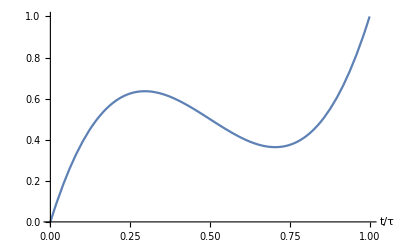

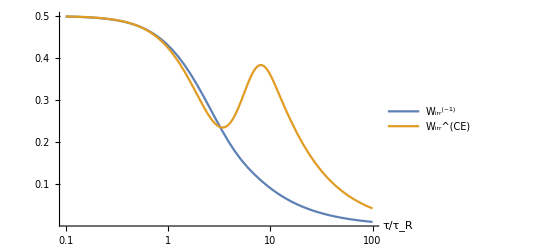

```mathematica
γ=1;
ω0=1;
τR=γ/ω0^2;
a=-1;

Plot[a(t-1/2)+4(1-a)(t-1/2)^3+1/2,{t,0,1},PlotRange->{{0,1},{0,1}},AxesLabel->{"t/τ"}]

LogLinearPlot[{Legended[W0[τ],"W_irr^(-1)"],Legended[Wh3[τ],"W_irr^(CE)"],},{τ,0.1,100},PlotRange->Full,AxesLabel->{"τ/τ_R"},PlotLegends->Placed[{},{Right,Center}]]
Clear[τR,γ,ω0,a,b]
```